```mathematica
bm
```

{{10000,0.000810524,-0.0873094,-0.108509},{20000,-0.164418,-0.163772,-0.167749},{30000,-0.213623,-0.0735539,-0.207947},{40000,-0.160675,-0.0963365,-0.224642},{50000,-0.0598456,-0.0654758,-0.092283},{60000,-0.16435,-0.13391,-0.193338},{70000,-0.158866,-0.0946628,-0.230386},{80000,-0.131921,-0.189751,-0.168366},{90000,-0.189976,-0.15925,-0.138689},{100000,-0.0356246,-0.130675,-0.0474232},{110000,-0.141884,-0.178872,-0.169269},{150000,-0.0863753,-0.0491186,-0.0715675}}

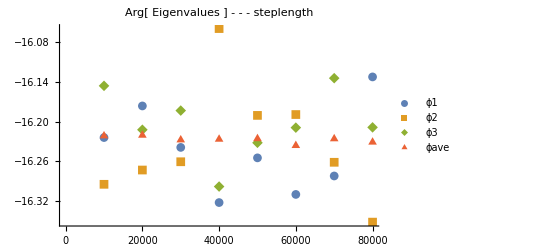

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_nMeas_ll_10_new","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - steplength"]
```

```mathematica
0.0025*13/3*2*π
0.0025*31/3*2*π
```

0.0680678

0.162316